```mathematica
Get["/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/QuantumWalks.wl"]
```

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Sacando la distribución de probabilidad con vectores de estado

Primero calculamos la caminata

```mathematica
statef=DTQW[{{1/Sqrt[2.],0,0},{ⅈ/Sqrt[2.],1,0}},100]//Chop;
```

```mathematica
coinB=IdentityMatrix[2];
posB=IdentityMatrix[201];
```

```mathematica
statefVec=Sum[i[[1]] KroneckerProduct[{coinB[[i[[2]]+1]]},{posB[[i[[3]]+101]]}],{i,#}]&@statef;
```

```mathematica
result=MatrixPartialTrace[statefVec†.statefVec,1,{2,201}]
```

```mathematica
Total@Abs@Diagonal@result
```

1.

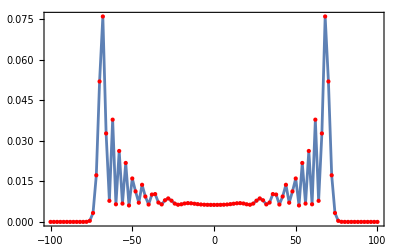

```mathematica
ListLinePlot[{Range[-100,100,2],(Abs@Diagonal@result)[[;;;;2]]}ᵀ,
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
MeshStyle->Directive[PointSize[Medium],Red],
ImageSize->Full
]
```

## Matriz de densidad

```mathematica
DTQW[{{1/2.,0,0,0,0},{ⅈ/2.,0,0,1,0},{ⅈ/2.,1,0,0,0},{1/2.,1,0,1,0}},100,2]//Chop
```

```mathematica
DTQW[{{1/2.,0,0,0,0},{ⅈ/2.,0,0,1,0},{ⅈ/2.,1,0,0,0},{1/2.,1,0,1,0}},10,2]//AbsoluteTiming
```

{0.257031,{{0.000976563+0.000976563 ⅈ,0,10,0,10},{0.000976563+0.000976563 ⅈ,0,10,1,8},{0.000976563+0.000976563 ⅈ,1,8,0,10},{0.000976563+0.000976563 ⅈ,1,8,1,8},{0.0078125+0.0078125 ⅈ,0,10,0,8},{0.00585938+0.00585938 ⅈ,0,10,1,6},{0.0078125+0.0078125 ⅈ,1,8,0,8},{0.00585938+0.00585938 ⅈ,1,8,1,6},{0.0078125+0.0078125 ⅈ,0,8,0,10},{0.0078125+0.0078125 ⅈ,0,8,1,8},{0.00585938+0.00585938 ⅈ,1,6,0,10},{0.00585938+0.00585938 ⅈ,1,6,1,8},{0.0634766+0.0615234 ⅈ,0,8,0,8},{0.0478516+0.0458984 ⅈ,0,8,1,6},{0.0478516+0.0458984 ⅈ,1,6,0,8},{0.0361328+0.0341797 ⅈ,1,6,1,6},{0.0136719+0.0136719 ⅈ,0,10,0,6},{0.00390625+0.00390625 ⅈ,0,10,1,4},{0.0136719+0.0136719 ⅈ,1,8,0,6},{0.00390625+0.00390625 ⅈ,1,8,1,4},{0.115234+0.103516 ⅈ,0,8,0,6},{0.0351563+0.0273438 ⅈ,0,8,1,4},{0.0878906+0.0761719 ⅈ,1,6,0,6},{0.0273438+0.0195313 ⅈ,1,6,1,4},{0.0136719+0.0136719 ⅈ,0,6,0,10},{0.0136719+0.0136719 ⅈ,0,6,1,8},{0.00390625+0.00390625 ⅈ,1,4,0,10},{0.00390625+0.00390625 ⅈ,1,4,1,8},{0.115234+0.103516 ⅈ,0,6,0,8},{0.0878906+0.0761719 ⅈ,0,6,1,6},{0.0351563+0.0273438 ⅈ,1,4,0,8},{0.0273438+0.0195313 ⅈ,1,4,1,6},{0.226563+0.15625 ⅈ,0,6,0,6},{0.078125+0.03125 ⅈ,0,6,1,4},{0.078125+0.03125 ⅈ,1,4,0,6},{0.03125+0. ⅈ,1,4,1,4},{-0.00390625-0.00390625 ⅈ,0,10,0,4},{-0.00585938-0.00585938 ⅈ,0,10,1,2},{-0.00390625-0.00390625 ⅈ,1,8,0,4},{-0.00585938-0.00585938 ⅈ,1,8,1,2},{-0.0273438-0.0351563 ⅈ,0,8,0,4},{-0.0488281-0.0449219 ⅈ,0,8,1,2},{-0.0195313-0.0273438 ⅈ,1,6,0,4},{-0.0371094-0.0332031 ⅈ,1,6,1,2},{-0.03125-0.078125 ⅈ,0,6,0,4},{-0.09375-0.0703125 ⅈ,0,6,1,2},{0.-0.03125 ⅈ,1,4,0,4},{-0.03125-0.015625 ⅈ,1,4,1,2},{-0.00390625-0.00390625 ⅈ,0,4,0,10},{-0.00390625-0.00390625 ⅈ,0,4,1,8},{-0.00585938-0.00585938 ⅈ,1,2,0,10},{-0.00585938-0.00585938 ⅈ,1,2,1,8},{-0.0273438-0.0351563 ⅈ,0,4,0,8},{-0.0195313-0.0273438 ⅈ,0,4,1,6},{-0.0488281-0.0449219 ⅈ,1,2,0,8},{-0.0371094-0.0332031 ⅈ,1,2,1,6},{-0.03125-0.078125 ⅈ,0,4,0,6},{0.-0.03125 ⅈ,0,4,1,4},{-0.09375-0.0703125 ⅈ,1,2,0,6},{-0.03125-0.015625 ⅈ,1,2,1,4},{0.03125+0. ⅈ,0,4,0,4},{0.015625+0.03125 ⅈ,0,4,1,2},{0.015625+0.03125 ⅈ,1,2,0,4},{0.0390625+0.03125 ⅈ,1,2,1,2},{0.00585938+0.00585938 ⅈ,0,10,1,0},{0.00585938+0.00585938 ⅈ,1,8,1,0},{-0.00585938+0.00585938 ⅈ,0,8,0,2},{0.046875+0.046875 ⅈ,0,8,1,0},{-0.00585938+0.00585938 ⅈ,1,6,0,2},{0.0351563+0.0351563 ⅈ,1,6,1,0},{-0.0351563+0.0351563 ⅈ,0,6,0,2},{0.0820313+0.0820313 ⅈ,0,6,1,0},{-0.0234375+0.0234375 ⅈ,1,4,0,2},{0.0234375+0.0234375 ⅈ,1,4,1,0},{-0.0234375+0.0234375 ⅈ,0,4,0,2},{-0.0234375-0.0234375 ⅈ,0,4,1,0},{0.0117188-0.0117188 ⅈ,1,2,0,2},{-0.0351563-0.0351563 ⅈ,1,2,1,0},{0.00585938+0.00585938 ⅈ,1,0,0,10},{0.00585938+0.00585938 ⅈ,1,0,1,8},{-0.00585938+0.00585938 ⅈ,0,2,0,8},{-0.00585938+0.00585938 ⅈ,0,2,1,6},{0.046875+0.046875 ⅈ,1,0,0,8},{0.0351563+0.0351563 ⅈ,1,0,1,6},{-0.0351563+0.0351563 ⅈ,0,2,0,6},{-0.0234375+0.0234375 ⅈ,0,2,1,4},{0.0820313+0.0820313 ⅈ,1,0,0,6},{0.0234375+0.0234375 ⅈ,1,0,1,4},{-0.0234375+0.0234375 ⅈ,0,2,0,4},{0.0117188-0.0117188 ⅈ,0,2,1,2},{-0.0234375-0.0234375 ⅈ,1,0,0,4},{-0.0351563-0.0351563 ⅈ,1,0,1,2},{0.0351563-0.0351563 ⅈ,0,2,0,2},{0.0351563+0.0351563 ⅈ,1,0,1,0},{0.00585938-0.00585938 ⅈ,0,8,0,0},{-0.046875-0.046875 ⅈ,0,8,1,-2},{0.00585938-0.00585938 ⅈ,1,6,0,0},{-0.0351563-0.0351563 ⅈ,1,6,1,-2},{0.0351563-0.0351563 ⅈ,0,6,0,0},{-0.0820313-0.0820313 ⅈ,0,6,1,-2},{0.0234375-0.0234375 ⅈ,1,4,0,0},{-0.0234375-0.0234375 ⅈ,1,4,1,-2},{0.0234375-0.0234375 ⅈ,0,4,0,0},{0.0234375+0.0234375 ⅈ,0,4,1,-2},{-0.0117188+0.0117188 ⅈ,1,2,0,0},{0.0351563+0.0351563 ⅈ,1,2,1,-2},{-0.0351563+0.0351563 ⅈ,0,2,0,0},{-0.0351563-0.0351563 ⅈ,1,0,1,-2},{0.00585938-0.00585938 ⅈ,0,0,0,8},{0.00585938-0.00585938 ⅈ,0,0,1,6},{-0.046875-0.046875 ⅈ,1,-2,0,8},{-0.0351563-0.0351563 ⅈ,1,-2,1,6},{0.0351563-0.0351563 ⅈ,0,0,0,6},{0.0234375-0.0234375 ⅈ,0,0,1,4},{-0.0820313-0.0820313 ⅈ,1,-2,0,6},{-0.0234375-0.0234375 ⅈ,1,-2,1,4},{0.0234375-0.0234375 ⅈ,0,0,0,4},{-0.0117188+0.0117188 ⅈ,0,0,1,2},{0.0234375+0.0234375 ⅈ,1,-2,0,4},{0.0351563+0.0351563 ⅈ,1,-2,1,2},{-0.0351563+0.0351563 ⅈ,0,0,0,2},{-0.0351563-0.0351563 ⅈ,1,-2,1,0},{0.0351563-0.0351563 ⅈ,0,0,0,0},{0.0351563+0.0351563 ⅈ,1,-2,1,-2},{-0.00585938-0.00585938 ⅈ,0,10,1,-2},{-0.00585938-0.00585938 ⅈ,1,8,1,-2},{0.00195313+0.00195313 ⅈ,0,10,0,-2},{0.00390625+0.00390625 ⅈ,0,10,1,-4},{0.00195313+0.00195313 ⅈ,1,8,0,-2},{0.00390625+0.00390625 ⅈ,1,8,1,-4},{0.00976563+0.0214844 ⅈ,0,8,0,-2},{0.0351563+0.0273438 ⅈ,0,8,1,-4},{0.00585938+0.0175781 ⅈ,1,6,0,-2},{0.0273438+0.0195313 ⅈ,1,6,1,-4},{-0.0078125+0.0625 ⅈ,0,6,0,-2},{0.078125+0.03125 ⅈ,0,6,1,-4},{-0.015625+0.03125 ⅈ,1,4,0,-2},{0.03125+0. ⅈ,1,4,1,-4},{-0.03125+0.015625 ⅈ,0,4,0,-2},{0.-0.03125 ⅈ,0,4,1,-4},{0.-0.0234375 ⅈ,1,2,0,-2},{-0.03125-0.015625 ⅈ,1,2,1,-4},{0.0351563-0.0351563 ⅈ,0,2,0,-2},{-0.0234375+0.0234375 ⅈ,0,2,1,-4},{0.0117188+0.0117188 ⅈ,1,0,0,-2},{0.0234375+0.0234375 ⅈ,1,0,1,-4},{-0.0351563+0.0351563 ⅈ,0,0,0,-2},{0.0234375-0.0234375 ⅈ,0,0,1,-4},{-0.0117188-0.0117188 ⅈ,1,-2,0,-2},{-0.0234375-0.0234375 ⅈ,1,-2,1,-4},{-0.00585938-0.00585938 ⅈ,1,-2,0,10},{-0.00585938-0.00585938 ⅈ,1,-2,1,8},{0.00195313+0.00195313 ⅈ,0,-2,0,10},{0.00195313+0.00195313 ⅈ,0,-2,1,8},{0.00390625+0.00390625 ⅈ,1,-4,0,10},{0.00390625+0.00390625 ⅈ,1,-4,1,8},{0.00976563+0.0214844 ⅈ,0,-2,0,8},{0.00585938+0.0175781 ⅈ,0,-2,1,6},{0.0351563+0.0273438 ⅈ,1,-4,0,8},{0.0273438+0.0195313 ⅈ,1,-4,1,6},{-0.0078125+0.0625 ⅈ,0,-2,0,6},{-0.015625+0.03125 ⅈ,0,-2,1,4},{0.078125+0.03125 ⅈ,1,-4,0,6},{0.03125+0. ⅈ,1,-4,1,4},{-0.03125+0.015625 ⅈ,0,-2,0,4},{0.-0.0234375 ⅈ,0,-2,1,2},{0.-0.03125 ⅈ,1,-4,0,4},{-0.03125-0.015625 ⅈ,1,-4,1,2},{0.0351563-0.0351563 ⅈ,0,-2,0,2},{0.0117188+0.0117188 ⅈ,0,-2,1,0},{-0.0234375+0.0234375 ⅈ,1,-4,0,2},{0.0234375+0.0234375 ⅈ,1,-4,1,0},{-0.0351563+0.0351563 ⅈ,0,-2,0,0},{-0.0117188-0.0117188 ⅈ,0,-2,1,-2},{0.0234375-0.0234375 ⅈ,1,-4,0,0},{-0.0234375-0.0234375 ⅈ,1,-4,1,-2},{0.0390625-0.03125 ⅈ,0,-2,0,-2},{-0.015625+0.03125 ⅈ,0,-2,1,-4},{-0.015625+0.03125 ⅈ,1,-4,0,-2},{0.03125+0. ⅈ,1,-4,1,-4},{-0.0273438-0.0351563 ⅈ,0,8,0,-4},{0.0332031+0.0605469 ⅈ,0,8,1,-6},{-0.0195313-0.0273438 ⅈ,1,6,0,-4},{0.0214844+0.0488281 ⅈ,1,6,1,-6},{-0.03125-0.078125 ⅈ,0,6,0,-4},{0.+0.164063 ⅈ,0,6,1,-6},{0.-0.03125 ⅈ,1,4,0,-4},{-0.03125+0.078125 ⅈ,1,4,1,-6},{0.03125+0. ⅈ,0,4,0,-4},{-0.078125+0.03125 ⅈ,0,4,1,-6},{0.015625+0.03125 ⅈ,1,2,0,-4},{-0.0078125-0.0625 ⅈ,1,2,1,-6},{-0.0234375+0.0234375 ⅈ,0,2,0,-4},{0.0820313-0.0820313 ⅈ,0,2,1,-6},{-0.0234375-0.0234375 ⅈ,1,0,0,-4},{0.0351563+0.0351563 ⅈ,1,0,1,-6},{0.0234375-0.0234375 ⅈ,0,0,0,-4},{-0.0820313+0.0820313 ⅈ,0,0,1,-6},{0.0234375+0.0234375 ⅈ,1,-2,0,-4},{-0.0351563-0.0351563 ⅈ,1,-2,1,-6},{-0.03125+0.015625 ⅈ,0,-2,0,-4},{0.09375-0.0703125 ⅈ,0,-2,1,-6},{0.-0.03125 ⅈ,1,-4,0,-4},{-0.03125+0.078125 ⅈ,1,-4,1,-6},{-0.0273438-0.0351563 ⅈ,0,-4,0,8},{-0.0195313-0.0273438 ⅈ,0,-4,1,6},{0.0332031+0.0605469 ⅈ,1,-6,0,8},{0.0214844+0.0488281 ⅈ,1,-6,1,6},{-0.03125-0.078125 ⅈ,0,-4,0,6},{0.-0.03125 ⅈ,0,-4,1,4},{0.+0.164063 ⅈ,1,-6,0,6},{-0.03125+0.078125 ⅈ,1,-6,1,4},{0.03125+0. ⅈ,0,-4,0,4},{0.015625+0.03125 ⅈ,0,-4,1,2},{-0.078125+0.03125 ⅈ,1,-6,0,4},{-0.0078125-0.0625 ⅈ,1,-6,1,2},{-0.0234375+0.0234375 ⅈ,0,-4,0,2},{-0.0234375-0.0234375 ⅈ,0,-4,1,0},{0.0820313-0.0820313 ⅈ,1,-6,0,2},{0.0351563+0.0351563 ⅈ,1,-6,1,0},{0.0234375-0.0234375 ⅈ,0,-4,0,0},{0.0234375+0.0234375 ⅈ,0,-4,1,-2},{-0.0820313+0.0820313 ⅈ,1,-6,0,0},{-0.0351563-0.0351563 ⅈ,1,-6,1,-2},{-0.03125+0.015625 ⅈ,0,-4,0,-2},{0.-0.03125 ⅈ,0,-4,1,-4},{0.09375-0.0703125 ⅈ,1,-6,0,-2},{-0.03125+0.078125 ⅈ,1,-6,1,-4},{0.03125+0. ⅈ,0,-4,0,-4},{-0.078125+0.03125 ⅈ,0,-4,1,-6},{-0.078125+0.03125 ⅈ,1,-6,0,-4},{0.226563-0.15625 ⅈ,1,-6,1,-6},{-0.00390625-0.00390625 ⅈ,0,10,0,-4},{0.00585938+0.00585938 ⅈ,0,10,1,-6},{-0.00390625-0.00390625 ⅈ,1,8,0,-4},{0.00585938+0.00585938 ⅈ,1,8,1,-6},{-0.000976563-0.000976563 ⅈ,0,10,0,-6},{0.000976563+0.000976563 ⅈ,0,10,1,-8},{-0.000976563-0.000976563 ⅈ,1,8,0,-6},{0.000976563+0.000976563 ⅈ,1,8,1,-8},{-0.00195313-0.0136719 ⅈ,0,8,0,-6},{0.+0.015625 ⅈ,0,8,1,-8},{0.-0.0117188 ⅈ,1,6,0,-6},{-0.00195313+0.0136719 ⅈ,1,6,1,-8},{0.0214844-0.0488281 ⅈ,0,6,0,-6},{-0.0332031+0.0605469 ⅈ,0,6,1,-8},{0.0195313-0.0273438 ⅈ,1,4,0,-6},{-0.0273438+0.0351563 ⅈ,1,4,1,-8},{0.0273438-0.0195313 ⅈ,0,4,0,-6},{-0.0351563+0.0273438 ⅈ,0,4,1,-8},{-0.00585938+0.0175781 ⅈ,1,2,0,-6},{0.00976563-0.0214844 ⅈ,1,2,1,-8},{-0.0351563+0.0351563 ⅈ,0,2,0,-6},{0.046875-0.046875 ⅈ,0,2,1,-8},{-0.00585938-0.00585938 ⅈ,1,0,0,-6},{0.00585938+0.00585938 ⅈ,1,0,1,-8},{0.0351563-0.0351563 ⅈ,0,0,0,-6},{-0.046875+0.046875 ⅈ,0,0,1,-8},{0.00585938+0.00585938 ⅈ,1,-2,0,-6},{-0.00585938-0.00585938 ⅈ,1,-2,1,-8},{-0.0371094+0.0332031 ⅈ,0,-2,0,-6},{0.0488281-0.0449219 ⅈ,0,-2,1,-8},{0.0195313-0.0273438 ⅈ,1,-4,0,-6},{-0.0273438+0.0351563 ⅈ,1,-4,1,-8},{0.0273438-0.0195313 ⅈ,0,-4,0,-6},{-0.0351563+0.0273438 ⅈ,0,-4,1,-8},{-0.0878906+0.0761719 ⅈ,1,-6,0,-6},{0.115234-0.103516 ⅈ,1,-6,1,-8},{-0.00390625-0.00390625 ⅈ,0,-4,0,10},{-0.00390625-0.00390625 ⅈ,0,-4,1,8},{0.00585938+0.00585938 ⅈ,1,-6,0,10},{0.00585938+0.00585938 ⅈ,1,-6,1,8},{-0.000976563-0.000976563 ⅈ,0,-6,0,10},{-0.000976563-0.000976563 ⅈ,0,-6,1,8},{0.000976563+0.000976563 ⅈ,1,-8,0,10},{0.000976563+0.000976563 ⅈ,1,-8,1,8},{-0.00195313-0.0136719 ⅈ,0,-6,0,8},{0.-0.0117188 ⅈ,0,-6,1,6},{0.+0.015625 ⅈ,1,-8,0,8},{-0.00195313+0.0136719 ⅈ,1,-8,1,6},{0.0214844-0.0488281 ⅈ,0,-6,0,6},{0.0195313-0.0273438 ⅈ,0,-6,1,4},{-0.0332031+0.0605469 ⅈ,1,-8,0,6},{-0.0273438+0.0351563 ⅈ,1,-8,1,4},{0.0273438-0.0195313 ⅈ,0,-6,0,4},{-0.00585938+0.0175781 ⅈ,0,-6,1,2},{-0.0351563+0.0273438 ⅈ,1,-8,0,4},{0.00976563-0.0214844 ⅈ,1,-8,1,2},{-0.0351563+0.0351563 ⅈ,0,-6,0,2},{-0.00585938-0.00585938 ⅈ,0,-6,1,0},{0.046875-0.046875 ⅈ,1,-8,0,2},{0.00585938+0.00585938 ⅈ,1,-8,1,0},{0.0351563-0.0351563 ⅈ,0,-6,0,0},{0.00585938+0.00585938 ⅈ,0,-6,1,-2},{-0.046875+0.046875 ⅈ,1,-8,0,0},{-0.00585938-0.00585938 ⅈ,1,-8,1,-2},{-0.0371094+0.0332031 ⅈ,0,-6,0,-2},{0.0195313-0.0273438 ⅈ,0,-6,1,-4},{0.0488281-0.0449219 ⅈ,1,-8,0,-2},{-0.0273438+0.0351563 ⅈ,1,-8,1,-4},{0.0273438-0.0195313 ⅈ,0,-6,0,-4},{-0.0878906+0.0761719 ⅈ,0,-6,1,-6},{-0.0351563+0.0273438 ⅈ,1,-8,0,-4},{0.115234-0.103516 ⅈ,1,-8,1,-6},{0.0361328-0.0341797 ⅈ,0,-6,0,-6},{-0.0478516+0.0458984 ⅈ,0,-6,1,-8},{-0.0478516+0.0458984 ⅈ,1,-8,0,-6},{0.0634766-0.0615234 ⅈ,1,-8,1,-8},{0.000976563-0.000976563 ⅈ,0,8,0,-8},{-0.000976563+0.000976563 ⅈ,0,8,1,-10},{0.000976563-0.000976563 ⅈ,1,6,0,-8},{-0.000976563+0.000976563 ⅈ,1,6,1,-10},{0.00585938-0.00585938 ⅈ,0,6,0,-8},{-0.00585938+0.00585938 ⅈ,0,6,1,-10},{0.00390625-0.00390625 ⅈ,1,4,0,-8},{-0.00390625+0.00390625 ⅈ,1,4,1,-10},{0.00390625-0.00390625 ⅈ,0,4,0,-8},{-0.00390625+0.00390625 ⅈ,0,4,1,-10},{-0.00195313+0.00195313 ⅈ,1,2,0,-8},{0.00195313-0.00195313 ⅈ,1,2,1,-10},{-0.00585938+0.00585938 ⅈ,0,2,0,-8},{0.00585938-0.00585938 ⅈ,0,2,1,-10},{0.00585938-0.00585938 ⅈ,0,0,0,-8},{-0.00585938+0.00585938 ⅈ,0,0,1,-10},{-0.00585938+0.00585938 ⅈ,0,-2,0,-8},{0.00585938-0.00585938 ⅈ,0,-2,1,-10},{0.00390625-0.00390625 ⅈ,1,-4,0,-8},{-0.00390625+0.00390625 ⅈ,1,-4,1,-10},{0.00390625-0.00390625 ⅈ,0,-4,0,-8},{-0.00390625+0.00390625 ⅈ,0,-4,1,-10},{-0.0136719+0.0136719 ⅈ,1,-6,0,-8},{0.0136719-0.0136719 ⅈ,1,-6,1,-10},{0.00585938-0.00585938 ⅈ,0,-6,0,-8},{-0.00585938+0.00585938 ⅈ,0,-6,1,-10},{-0.0078125+0.0078125 ⅈ,1,-8,0,-8},{0.0078125-0.0078125 ⅈ,1,-8,1,-10},{0.000976563-0.000976563 ⅈ,0,-8,0,8},{0.000976563-0.000976563 ⅈ,0,-8,1,6},{-0.000976563+0.000976563 ⅈ,1,-10,0,8},{-0.000976563+0.000976563 ⅈ,1,-10,1,6},{0.00585938-0.00585938 ⅈ,0,-8,0,6},{0.00390625-0.00390625 ⅈ,0,-8,1,4},{-0.00585938+0.00585938 ⅈ,1,-10,0,6},{-0.00390625+0.00390625 ⅈ,1,-10,1,4},{0.00390625-0.00390625 ⅈ,0,-8,0,4},{-0.00195313+0.00195313 ⅈ,0,-8,1,2},{-0.00390625+0.00390625 ⅈ,1,-10,0,4},{0.00195313-0.00195313 ⅈ,1,-10,1,2},{-0.00585938+0.00585938 ⅈ,0,-8,0,2},{0.00585938-0.00585938 ⅈ,1,-10,0,2},{0.00585938-0.00585938 ⅈ,0,-8,0,0},{-0.00585938+0.00585938 ⅈ,1,-10,0,0},{-0.00585938+0.00585938 ⅈ,0,-8,0,-2},{0.00390625-0.00390625 ⅈ,0,-8,1,-4},{0.00585938-0.00585938 ⅈ,1,-10,0,-2},{-0.00390625+0.00390625 ⅈ,1,-10,1,-4},{0.00390625-0.00390625 ⅈ,0,-8,0,-4},{-0.0136719+0.0136719 ⅈ,0,-8,1,-6},{-0.00390625+0.00390625 ⅈ,1,-10,0,-4},{0.0136719-0.0136719 ⅈ,1,-10,1,-6},{0.00585938-0.00585938 ⅈ,0,-8,0,-6},{-0.0078125+0.0078125 ⅈ,0,-8,1,-8},{-0.00585938+0.00585938 ⅈ,1,-10,0,-6},{0.0078125-0.0078125 ⅈ,1,-10,1,-8},{0.000976563-0.000976563 ⅈ,0,-8,0,-8},{-0.000976563+0.000976563 ⅈ,0,-8,1,-10},{-0.000976563+0.000976563 ⅈ,1,-10,0,-8},{0.000976563-0.000976563 ⅈ,1,-10,1,-10}}}

```mathematica
201*201
```

40401

```mathematica
Dimensions@%45
```

{39984,5}

## TODO

Notación de JA para que devuelva un vector

Constuir el operador de moneda

Construir el operador Shift

Construir la caminata entera